```mathematica
(*3*)
```

```mathematica
(*1.)U^.08e(x)*)
```

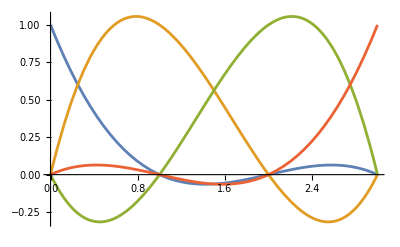

```mathematica
n=4;
Ue[k_] := Sum[Symbol["c"<>ToString[i]]*x^(i-1),{i,1,k}];
generateMatrix[N_]:=Table[x[i]^(j-1),{i,N},{j,N}];
generateCVector[N_]:=Table[Symbol["c"<>ToString[i]],{i,N}];
generateUeVector[N_]:=Table[Symbol["U"<>ToString[i]],{i,N}];
 M = generateMatrix[n];
Cn= generateCVector[n];
Un = generateUeVector[n];
Csol= LinearSolve[M, Un];
CwithSolution=Thread[Cn->Csol];
UFunc=Coefficient[Collect[Simplify[Sum[Cn[[i]] x^(i-1),{i,n}]/. CwithSolution], Un], Un];
CRR[N_]:=Table[x[i]->(i-1),{i,1,N}];
result =UFunc/.CRR[n];
Plot[result, {x,0,n-1}]
```

```mathematica
(*2.*)
```